# Notebook 12: Images

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Images

The most common kind of raster graphics are images created by digital photography (including digital scanning of analog images)

Mathematica has a number of built-in images that can be retrieved with the ExampleData command, listed below. We will use two of them as our examples.

```mathematica
ExampleData["TestImage"]
```

{{TestImage,Aerial},{TestImage,Aerial2},{TestImage,Airplane},{TestImage,Airplane2},{TestImage,Airport},{TestImage,APC},{TestImage,Apples},{TestImage,Boat},{TestImage,Bridge},{TestImage,CarAndAPC},{TestImage,CarAndAPC2},{TestImage,ChemicalPlant},{TestImage,Clock},{TestImage,Couple},{TestImage,Couple2},{TestImage,Elaine},{TestImage,F16},{TestImage,Flower},{TestImage,Girl},{TestImage,Girl2},{TestImage,Girl3},{TestImage,Gray21},{TestImage,House},{TestImage,House2},{TestImage,JellyBeans},{TestImage,JellyBeans2},{TestImage,Lena},{TestImage,Man},{TestImage,Mandrill},{TestImage,Marruecos},{TestImage,Moon},{TestImage,Numbers},{TestImage,Peppers},{TestImage,RadcliffeCamera},{TestImage,ResolutionChart},{TestImage,Ruler},{TestImage,Sailboat},{TestImage,Splash},{TestImage,Stall},{TestImage,Tank},{TestImage,Tank2},{TestImage,Tank3},{TestImage,TestPattern},{TestImage,Tiffany},{TestImage,Tree},{TestImage,Truck},{TestImage,TruckAndAPC},{TestImage,TruckAndAPC2},{TestImage,U2},{TestImage,Volubilis}}

#### Sample grayscale image

```mathematica
grayscaleImage=ExampleData[{"TestImage","Couple2"}]
```

-Graphics-

#### Sample colour image

```mathematica
colourImage=ExampleData[{"TestImage","Apples"}]
```

-Graphics-

#### Image properties

We can retrieve many different properties of a digital image with the ImageMeasurements command

```mathematica
ImageMeasurements[grayscaleImage,{"ColorSpace","Dimensions","Channels"}]
```

{Grayscale,{512,512},1}

```mathematica
ImageMeasurements[colourImage,{"ColorSpace","Dimensions","Channels"}]
```

{RGB,{1800,2700,3},3}

There are individual commands corresponding to each property

```mathematica
ImageColorSpace[grayscaleImage]
```

Grayscale

```mathematica
ImageDimensions[grayscaleImage]
```

{512,512}

```mathematica
ImageChannels[grayscaleImage]
```

1

## Image Data

Images consist of rows and columns of pixels, numbered from the upper left hand corner. The ImageTake command allows us to extract a portion of an image. In this case, we are asking for rows 153 to 204, columns 278 to 321.

```mathematica
lady=ImageTake[grayscaleImage,{153,204},{278,321}]
```

-Graphics-

The resulting selection is 44 pixels wide and 52 pixels high.

```mathematica
ImageDimensions[lady]
```

{44,52}

Let’s take an even smaller portion of this image to look at the underlying data.

```mathematica
ladySmile=ImageTake[lady,{32,42},{10,20}]
```

-Graphics-

The MatrixForm command displays a nested list as rows and columns of data. These are the grayscale values for each pixel in the smile.

```mathematica
MatrixForm[ImageData[ladySmile]]
```

(0.67451 | 0.658824 | 0.611765 | 0.6 | 0.572549 | 0.556863 | 0.588235 | 0.65098 | 0.698039 | 0.647059 | 0.611765
0.623529 | 0.580392 | 0.611765 | 0.584314 | 0.552941 | 0.541176 | 0.517647 | 0.607843 | 0.678431 | 0.639216 | 0.615686
0.529412 | 0.521569 | 0.576471 | 0.486275 | 0.435294 | 0.447059 | 0.490196 | 0.560784 | 0.568627 | 0.607843 | 0.584314
0.454902 | 0.498039 | 0.6 | 0.584314 | 0.552941 | 0.564706 | 0.568627 | 0.560784 | 0.498039 | 0.541176 | 0.552941
0.482353 | 0.47451 | 0.517647 | 0.54902 | 0.564706 | 0.533333 | 0.541176 | 0.541176 | 0.494118 | 0.454902 | 0.486275
0.54902 | 0.537255 | 0.556863 | 0.556863 | 0.611765 | 0.611765 | 0.501961 | 0.407843 | 0.368627 | 0.47451 | 0.517647
0.564706 | 0.552941 | 0.580392 | 0.501961 | 0.560784 | 0.533333 | 0.447059 | 0.466667 | 0.541176 | 0.588235 | 0.564706
0.54902 | 0.552941 | 0.588235 | 0.52549 | 0.505882 | 0.494118 | 0.498039 | 0.54902 | 0.556863 | 0.564706 | 0.533333
0.541176 | 0.560784 | 0.611765 | 0.592157 | 0.603922 | 0.603922 | 0.568627 | 0.576471 | 0.568627 | 0.564706 | 0.529412
0.54902 | 0.54902 | 0.584314 | 0.611765 | 0.647059 | 0.639216 | 0.576471 | 0.576471 | 0.568627 | 0.545098 | 0.494118
0.54902 | 0.576471 | 0.568627 | 0.560784 | 0.568627 | 0.560784 | 0.529412 | 0.517647 | 0.494118 | 0.45098 | 0.423529)

This is the pixel value in the upper left hand corner of the ladySmile image

```mathematica
ImageData[ladySmile]⟦1,1⟧
```

0.67451

If we use the same value for all three components of RGBColor, we can see a paint chip

```mathematica
RGBColor[0.67451,0.67451,0.67451]
```

RGBColor[0.67451, 0.67451, 0.67451]

We can also see the first row as a Raster.

```mathematica
ImageData[ladySmile]⟦1⟧
```

{0.67451,0.658824,0.611765,0.6,0.572549,0.556863,0.588235,0.65098,0.698039,0.647059,0.611765}

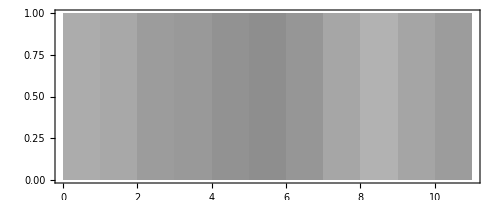

```mathematica
Graphics[Raster[{ImageData[ladySmile]⟦1⟧}],Frame->True]
```

#### Part of a colour image

Here is a small portion of the apple image. It is a piece of one of the stems.

```mathematica
appleStem=ImageTake[colourImage,{1055,1065},{855,865}]
```

-Graphics-

Since this is a colour image, each pixel is represented by three numbers: red, green and blue components. Another way of saying this is that the image has three channels. (A colour image may also have a channel for opacity / transparency, but this one does not).

```mathematica
ImageColorSpace[appleStem]
```

RGB

```mathematica
ImageChannels[appleStem]
```

3

We can represent the image matrix in two ways. By default, the three colour channels are interleaved. That is to say, that each pixels is shown as a list of R, G and B values.

```mathematica
MatrixForm[ImageData[appleStem]]
```

((0.584314
0.392157
0.223529) | (0.54902
0.356863
0.196078) | (0.564706
0.372549
0.215686) | (0.533333
0.345098
0.196078) | (0.564706
0.384314
0.25098) | (0.466667
0.290196
0.160784) | (0.34902
0.188235
0.0705882) | (0.321569
0.184314
0.0745098) | (0.298039
0.164706
0.0666667) | (0.321569
0.196078
0.105882) | (0.286275
0.196078
0.0627451)
(0.572549
0.380392
0.219608) | (0.564706
0.372549
0.215686) | (0.54902
0.352941
0.207843) | (0.505882
0.309804
0.172549) | (0.619608
0.427451
0.301961) | (0.541176
0.364706
0.243137) | (0.360784
0.2
0.0901961) | (0.305882
0.160784
0.0588235) | (0.290196
0.156863
0.0588235) | (0.301961
0.176471
0.0862745) | (0.290196
0.2
0.0666667)
(0.603922
0.392157
0.207843) | (0.552941
0.34902
0.192157) | (0.501961
0.313725
0.172549) | (0.498039
0.321569
0.192157) | (0.588235
0.427451
0.309804) | (0.521569
0.384314
0.27451) | (0.341176
0.207843
0.109804) | (0.270588
0.14902
0.0666667) | (0.258824
0.145098
0.0823529) | (0.25098
0.137255
0.0823529) | (0.278431
0.188235
0.12549)
(0.635294
0.419608
0.207843) | (0.564706
0.360784
0.172549) | (0.541176
0.34902
0.180392) | (0.572549
0.396078
0.243137) | (0.627451
0.470588
0.333333) | (0.509804
0.368627
0.243137) | (0.329412
0.196078
0.0901961) | (0.282353
0.156863
0.0666667) | (0.270588
0.160784
0.0784314) | (0.262745
0.14902
0.0784314) | (0.27451
0.188235
0.105882)
(0.690196
0.47451
0.219608) | (0.627451
0.415686
0.180392) | (0.596078
0.403922
0.184314) | (0.658824
0.47451
0.294118) | (0.654902
0.482353
0.329412) | (0.470588
0.317647
0.188235) | (0.309804
0.172549
0.0627451) | (0.278431
0.152941
0.054902) | (0.278431
0.160784
0.0666667) | (0.262745
0.152941
0.0666667) | (0.286275
0.184314
0.0862745)
(0.760784
0.529412
0.231373) | (0.729412
0.509804
0.219608) | (0.686275
0.478431
0.219608) | (0.733333
0.541176
0.321569) | (0.639216
0.466667
0.290196) | (0.435294
0.266667
0.133333) | (0.309804
0.164706
0.0588235) | (0.290196
0.156863
0.0509804) | (0.27451
0.156863
0.0470588) | (0.270588
0.164706
0.0509804) | (0.305882
0.203922
0.0666667)
(0.796078
0.54902
0.235294) | (0.807843
0.576471
0.262745) | (0.772549
0.552941
0.262745) | (0.768627
0.564706
0.329412) | (0.607843
0.419608
0.239216) | (0.411765
0.235294
0.113725) | (0.337255
0.180392
0.0823529) | (0.313725
0.172549
0.0784314) | (0.290196
0.168627
0.054902) | (0.301961
0.188235
0.0627451) | (0.360784
0.247059
0.0745098)
(0.8
0.541176
0.211765) | (0.839216
0.584314
0.254902) | (0.815686
0.584314
0.278431) | (0.768627
0.552941
0.301961) | (0.568627
0.360784
0.188235) | (0.403922
0.207843
0.101961) | (0.352941
0.188235
0.101961) | (0.321569
0.172549
0.0823529) | (0.313725
0.180392
0.0705882) | (0.333333
0.215686
0.0745098) | (0.435294
0.321569
0.101961)
(0.811765
0.533333
0.211765) | (0.827451
0.568627
0.231373) | (0.839216
0.592157
0.278431) | (0.780392
0.545098
0.298039) | (0.564706
0.352941
0.180392) | (0.415686
0.215686
0.109804) | (0.384314
0.2
0.129412) | (0.352941
0.192157
0.105882) | (0.360784
0.223529
0.0980392) | (0.388235
0.262745
0.109804) | (0.509804
0.396078
0.129412)
(0.827451
0.541176
0.231373) | (0.819608
0.556863
0.215686) | (0.870588
0.615686
0.286275) | (0.811765
0.572549
0.309804) | (0.603922
0.384314
0.2) | (0.466667
0.258824
0.137255) | (0.423529
0.235294
0.145098) | (0.4
0.239216
0.121569) | (0.423529
0.286275
0.129412) | (0.454902
0.329412
0.137255) | (0.564706
0.45098
0.145098)
(0.831373
0.54902
0.227451) | (0.831373
0.568627
0.211765) | (0.862745
0.623529
0.27451) | (0.847059
0.615686
0.317647) | (0.643137
0.423529
0.2) | (0.486275
0.282353
0.12549) | (0.423529
0.243137
0.101961) | (0.454902
0.290196
0.12549) | (0.509804
0.372549
0.152941) | (0.603922
0.482353
0.227451) | (0.694118
0.588235
0.247059))

This is the pixel value in the upper left hand corner of the appleStem image

```mathematica
ImageData[appleStem]⟦1,1⟧
```

{0.584314,0.392157,0.223529}

We can use RGBColor to see a paint chip

```mathematica
RGBColor[{0.584314,0.392157,0.223529}]
```

RGBColor[{0.584314, 0.392157, 0.223529}]

We can also visualize the first row of appleStem using Raster

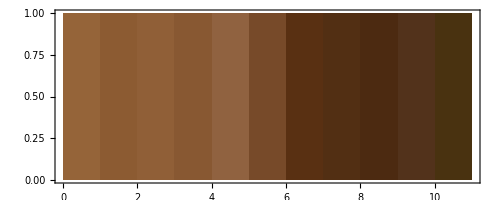

```mathematica
Graphics[Raster[{ImageData[appleStem]⟦1⟧}],Frame->True]
```

#### Colour separation

We have the option of visualizing a colour image as matrixes of Red, Green and Blue components if we wish. (The Map command will be introduced later, but we need it here to get the matrixes to display the way we want them.)

```mathematica
Map[MatrixForm,ImageData[appleStem,Interleaving->False]]
```

{(0.584314 | 0.54902 | 0.564706 | 0.533333 | 0.564706 | 0.466667 | 0.34902 | 0.321569 | 0.298039 | 0.321569 | 0.286275
0.572549 | 0.564706 | 0.54902 | 0.505882 | 0.619608 | 0.541176 | 0.360784 | 0.305882 | 0.290196 | 0.301961 | 0.290196
0.603922 | 0.552941 | 0.501961 | 0.498039 | 0.588235 | 0.521569 | 0.341176 | 0.270588 | 0.258824 | 0.25098 | 0.278431
0.635294 | 0.564706 | 0.541176 | 0.572549 | 0.627451 | 0.509804 | 0.329412 | 0.282353 | 0.270588 | 0.262745 | 0.27451
0.690196 | 0.627451 | 0.596078 | 0.658824 | 0.654902 | 0.470588 | 0.309804 | 0.278431 | 0.278431 | 0.262745 | 0.286275
0.760784 | 0.729412 | 0.686275 | 0.733333 | 0.639216 | 0.435294 | 0.309804 | 0.290196 | 0.27451 | 0.270588 | 0.305882
0.796078 | 0.807843 | 0.772549 | 0.768627 | 0.607843 | 0.411765 | 0.337255 | 0.313725 | 0.290196 | 0.301961 | 0.360784
0.8 | 0.839216 | 0.815686 | 0.768627 | 0.568627 | 0.403922 | 0.352941 | 0.321569 | 0.313725 | 0.333333 | 0.435294
0.811765 | 0.827451 | 0.839216 | 0.780392 | 0.564706 | 0.415686 | 0.384314 | 0.352941 | 0.360784 | 0.388235 | 0.509804
0.827451 | 0.819608 | 0.870588 | 0.811765 | 0.603922 | 0.466667 | 0.423529 | 0.4 | 0.423529 | 0.454902 | 0.564706
0.831373 | 0.831373 | 0.862745 | 0.847059 | 0.643137 | 0.486275 | 0.423529 | 0.454902 | 0.509804 | 0.603922 | 0.694118),(0.392157 | 0.356863 | 0.372549 | 0.345098 | 0.384314 | 0.290196 | 0.188235 | 0.184314 | 0.164706 | 0.196078 | 0.196078
0.380392 | 0.372549 | 0.352941 | 0.309804 | 0.427451 | 0.364706 | 0.2 | 0.160784 | 0.156863 | 0.176471 | 0.2
0.392157 | 0.34902 | 0.313725 | 0.321569 | 0.427451 | 0.384314 | 0.207843 | 0.14902 | 0.145098 | 0.137255 | 0.188235
0.419608 | 0.360784 | 0.34902 | 0.396078 | 0.470588 | 0.368627 | 0.196078 | 0.156863 | 0.160784 | 0.14902 | 0.188235
0.47451 | 0.415686 | 0.403922 | 0.47451 | 0.482353 | 0.317647 | 0.172549 | 0.152941 | 0.160784 | 0.152941 | 0.184314
0.529412 | 0.509804 | 0.478431 | 0.541176 | 0.466667 | 0.266667 | 0.164706 | 0.156863 | 0.156863 | 0.164706 | 0.203922
0.54902 | 0.576471 | 0.552941 | 0.564706 | 0.419608 | 0.235294 | 0.180392 | 0.172549 | 0.168627 | 0.188235 | 0.247059
0.541176 | 0.584314 | 0.584314 | 0.552941 | 0.360784 | 0.207843 | 0.188235 | 0.172549 | 0.180392 | 0.215686 | 0.321569
0.533333 | 0.568627 | 0.592157 | 0.545098 | 0.352941 | 0.215686 | 0.2 | 0.192157 | 0.223529 | 0.262745 | 0.396078
0.541176 | 0.556863 | 0.615686 | 0.572549 | 0.384314 | 0.258824 | 0.235294 | 0.239216 | 0.286275 | 0.329412 | 0.45098
0.54902 | 0.568627 | 0.623529 | 0.615686 | 0.423529 | 0.282353 | 0.243137 | 0.290196 | 0.372549 | 0.482353 | 0.588235),(0.223529 | 0.196078 | 0.215686 | 0.196078 | 0.25098 | 0.160784 | 0.0705882 | 0.0745098 | 0.0666667 | 0.105882 | 0.0627451
0.219608 | 0.215686 | 0.207843 | 0.172549 | 0.301961 | 0.243137 | 0.0901961 | 0.0588235 | 0.0588235 | 0.0862745 | 0.0666667
0.207843 | 0.192157 | 0.172549 | 0.192157 | 0.309804 | 0.27451 | 0.109804 | 0.0666667 | 0.0823529 | 0.0823529 | 0.12549
0.207843 | 0.172549 | 0.180392 | 0.243137 | 0.333333 | 0.243137 | 0.0901961 | 0.0666667 | 0.0784314 | 0.0784314 | 0.105882
0.219608 | 0.180392 | 0.184314 | 0.294118 | 0.329412 | 0.188235 | 0.0627451 | 0.054902 | 0.0666667 | 0.0666667 | 0.0862745
0.231373 | 0.219608 | 0.219608 | 0.321569 | 0.290196 | 0.133333 | 0.0588235 | 0.0509804 | 0.0470588 | 0.0509804 | 0.0666667
0.235294 | 0.262745 | 0.262745 | 0.329412 | 0.239216 | 0.113725 | 0.0823529 | 0.0784314 | 0.054902 | 0.0627451 | 0.0745098
0.211765 | 0.254902 | 0.278431 | 0.301961 | 0.188235 | 0.101961 | 0.101961 | 0.0823529 | 0.0705882 | 0.0745098 | 0.101961
0.211765 | 0.231373 | 0.278431 | 0.298039 | 0.180392 | 0.109804 | 0.129412 | 0.105882 | 0.0980392 | 0.109804 | 0.129412
0.231373 | 0.215686 | 0.286275 | 0.309804 | 0.2 | 0.137255 | 0.145098 | 0.121569 | 0.129412 | 0.137255 | 0.145098
0.227451 | 0.211765 | 0.27451 | 0.317647 | 0.2 | 0.12549 | 0.101961 | 0.12549 | 0.152941 | 0.227451 | 0.247059)}

Here is the matrix for the Red components. It is the first row of the matrix above.

```mathematica
MatrixForm[ImageData[appleStem,Interleaving->False]⟦1⟧]
```

(0.584314 | 0.54902 | 0.564706 | 0.533333 | 0.564706 | 0.466667 | 0.34902 | 0.321569 | 0.298039 | 0.321569 | 0.286275
0.572549 | 0.564706 | 0.54902 | 0.505882 | 0.619608 | 0.541176 | 0.360784 | 0.305882 | 0.290196 | 0.301961 | 0.290196
0.603922 | 0.552941 | 0.501961 | 0.498039 | 0.588235 | 0.521569 | 0.341176 | 0.270588 | 0.258824 | 0.25098 | 0.278431
0.635294 | 0.564706 | 0.541176 | 0.572549 | 0.627451 | 0.509804 | 0.329412 | 0.282353 | 0.270588 | 0.262745 | 0.27451
0.690196 | 0.627451 | 0.596078 | 0.658824 | 0.654902 | 0.470588 | 0.309804 | 0.278431 | 0.278431 | 0.262745 | 0.286275
0.760784 | 0.729412 | 0.686275 | 0.733333 | 0.639216 | 0.435294 | 0.309804 | 0.290196 | 0.27451 | 0.270588 | 0.305882
0.796078 | 0.807843 | 0.772549 | 0.768627 | 0.607843 | 0.411765 | 0.337255 | 0.313725 | 0.290196 | 0.301961 | 0.360784
0.8 | 0.839216 | 0.815686 | 0.768627 | 0.568627 | 0.403922 | 0.352941 | 0.321569 | 0.313725 | 0.333333 | 0.435294
0.811765 | 0.827451 | 0.839216 | 0.780392 | 0.564706 | 0.415686 | 0.384314 | 0.352941 | 0.360784 | 0.388235 | 0.509804
0.827451 | 0.819608 | 0.870588 | 0.811765 | 0.603922 | 0.466667 | 0.423529 | 0.4 | 0.423529 | 0.454902 | 0.564706
0.831373 | 0.831373 | 0.862745 | 0.847059 | 0.643137 | 0.486275 | 0.423529 | 0.454902 | 0.509804 | 0.603922 | 0.694118)

The ColorSeparate command shows us the Red, Green and Blue channels (i.e., component matrixes) separately. Since each channel consists of pixels with single real values, they appear as grayscale.

```mathematica
ColorSeparate[appleStem]
```

{-Graphics-,-Graphics-,-Graphics-}

## Image Colours

#### Histograms

One common way of representing the values or colours in an image is with a histogram. If we generate a histogram of a grayscale image, it shows us how many pixels of each value appear in the image. Most of the pixels in the picture of the couple have an intermediate level of gray (between .4 and .6).

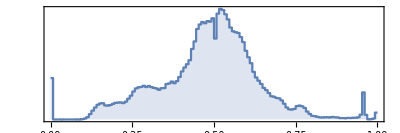

```mathematica
ImageHistogram[grayscaleImage]
```

When we look at the histogram for a colour image, we can see the intensities for the Red, Green and Blue channels separately.

Here is our picture of the apple stem

```mathematica
appleStem
```

-Graphics-

Here are the three separate channels, Red, Green and Blue

```mathematica
ColorSeparate[appleStem]
```

{-Graphics-,-Graphics-,-Graphics-}

Here is the corresponding histogram. Note that there are more pixels with high red and green values than with high blue ones.

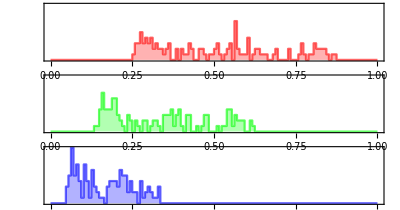

```mathematica
ImageHistogram[appleStem,Appearance->"Separated"]
```

Here is the histogram for our full-colour image of the apples.

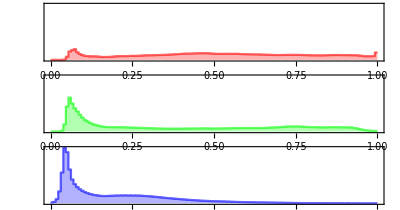

```mathematica
ImageHistogram[colourImage,Appearance->"Separated"]
```

#### Removing colour and value

We can reduce the number of colours in an coloured image with ColorQuantize. Here we are saying we only want four colours

```mathematica
fourColour=ColorQuantize[colourImage,4]
```

-Graphics-

This has a drastic effect on the histogram

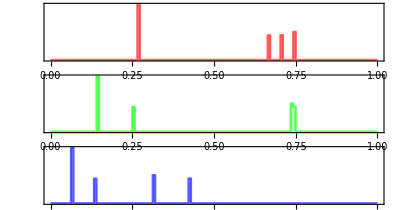

```mathematica
ImageHistogram[fourColour,Appearance->"Separated"]
```

Remember that each of the four colours in the image above has Red, Green and Blue components

```mathematica
ColorSeparate[fourColour]
```

{-Graphics-,-Graphics-,-Graphics-}

We can convert a colour image into grayscale with ColorConvert

```mathematica
ColorConvert[colourImage,"Grayscale"]
```

-Graphics-

We can convert a colour or grayscale image into black and white pixels with Binarize

```mathematica
Binarize[colourImage]
```

-Graphics-

```mathematica
Binarize[grayscaleImage]
```

-Graphics-

#### Adding colour

We can tint a grayscale image with Blend

```mathematica
Blend[{grayscaleImage,Pink}]
```

-Graphics-

We can also replace pixel values with pseudocolours using the Colorize command

```mathematica
Colorize[grayscaleImage]
```

-Graphics-

The Colorize command takes a ColorFunction argument that allows you to specify the spectrum of colours you want to map to grayscale values.

```mathematica
Colorize[grayscaleImage,ColorFunction->"RoseColors"]
```

-Graphics-

Here are some of the possible values for ColorFunction

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

## Image Manipulation

#### Thumbnails

Automatically generate thumbnail images

```mathematica
grayThumb=Thumbnail[grayscaleImage]
```

-Graphics-

```mathematica
colourThumb=Thumbnail[colourImage]
```

-Graphics-

#### Cropping

The ImageTrim command returns the smallest subimage containing specified points (N.B. this has a similar result to ImageTake but the coordinates are specified differently)

```mathematica
fellow=ImageTrim[grayscaleImage,{{153,330},{195,379}}]
```

-Graphics-

```mathematica
gSmith=ImageTrim[colourImage,{{810,1088},{1180,1488}}]
```

-Graphics-

```mathematica
ImageDimensions[gSmith]
```

{372,402}

#### Resizing

This example sets the width of the resized image, but you have a number of options

```mathematica
gSmithSmall=ImageResize[gSmith,120]
```

-Graphics-

```mathematica
ImageDimensions[gSmithSmall]
```

{120,130}

#### Reflecting

Top-bottom

```mathematica
ImageReflect[gSmithSmall]
```

-Graphics-

Left-right

```mathematica
ImageReflect[gSmithSmall,Left]
```

-Graphics-

#### Rotating

```mathematica
ImageRotate[gSmithSmall,45Degree]
```

-Graphics-

```mathematica
ImageRotate[gSmithSmall,90Degree]
```

-Graphics-

## Filtering and Effects

You can also apply a very wide variety of filters and Photoshop-style effects to your images

The second parameter of Blur is the pixel radius

```mathematica
Blur[gSmithSmall,10]
```

-Graphics-

```mathematica
ImageEffect[gSmithSmall,"OilPainting"]
```

-Graphics-

```mathematica
ImageEffect[gSmithSmall,"Posterization"]
```

-Graphics-

```mathematica
ImageEffect[gSmithSmall,"Comics"]
```

-Graphics-

```mathematica
ImageEffect[gSmithSmall,"Solarization"]
```

-Graphics-

```mathematica
ImageEffect[gSmithSmall,"MotionBlur"]
```

-Graphics-

## In-Class Activity

### Starting with any one of the built-in images from ExampleData, apply a number of transformations to it until it looks like abstract art.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course